Homework 7

Nhi Nguyen, Trang Nguyen, Melvin Chang

Problem 1

```mathematica
t:=RandomReal[{-1,1}];
```

```mathematica
step:={t,t}
```

```mathematica
step
```

{0.270716,-0.215352}

```mathematica
Norm[{0.2707163418512666,-0.21535197732899247}]
```

0.345925

```mathematica
N[Mean[Table[Norm[step],{100}]]]
```

0.720698

```mathematica
N[Mean[Table[Norm[step],{10^6}]]]
```

0.764595

Problem 2

```mathematica
c=2;
```

```mathematica
x=NestList[Sqrt[c+#]&,Sqrt[2],15]
```

{√2,√(2+√2),√(2+√(2+√2)),√(2+√(2+√(2+√2))),√(2+√(2+√(2+√(2+√2)))),√(2+√(2+√(2+√(2+√(2+√2))))),√(2+√(2+√(2+√(2+√(2+√(2+√2)))))),√(2+√(2+√(2+√(2+√(2+√(2+√(2+√2))))))),√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√2)))))))),√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√2))))))))),√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√2)))))))))),√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√2))))))))))),√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√2)))))))))))),√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√2))))))))))))),√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√2)))))))))))))),√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√2)))))))))))))))}

```mathematica
myFunction=ListPlot[x,PlotRange->{{0,15},{1,4}}];
asymtote=Plot[2,{x,0,15},PlotStyle->Dashed];
```

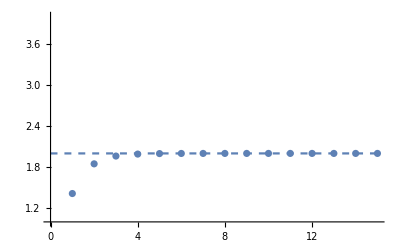

```mathematica
Show[myFunction,asymtote]
```